## 文字（云梦睡虎地秦简）、古钱币分析

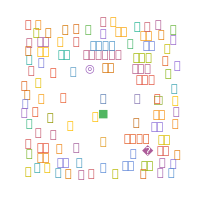

```mathematica
text=Import["https://zh.wikisource.org/wiki/%E7%9D%A1%E8%99%8E%E5%9C%B0%E7%A7%A6%E7%B0%A1"];
WordCloud[text]
```

```mathematica
铜钱={{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
FeatureSpacePlot[RandomSample[Flatten[铜钱]], LabelingSize -> 40,Axes->True]
```

-Graphics-

## 古文字演化

```mathematica
characters={"甲骨文","周代金文","篆文","隶书","楷书"};
characterImages = {{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
characterImagesSampled = RandomSample[Flatten[characterImages]];
```

```mathematica
extractorFunction=FeatureExtraction[characterImagesSampled]
```

FeatureExtractorFunction[…]

```mathematica
extractorFunction[-Graphics-]
```

{-28.0159,-33.2189,-26.0636,32.5759,10.9285,-15.2417,28.7536,0.552546,25.9671,-13.0088,-16.7053,41.8034,-11.153,1.16118,30.5676,-33.6933,-25.6253,6.27454,-7.52227,-6.19304,1.11165,33.3735,43.0963,-25.4414}

```mathematica
nearestFunction=FeatureNearest[characterImagesSampled]
```

NearestFunction[…]

```mathematica
nearestFunction[-Graphics-](*马王堆-隶书*)
```

{-Graphics-}

```mathematica
FeatureSpacePlot[characterImagesSampled, LabelingSize -> 40,Axes->True]
```

-Graphics-

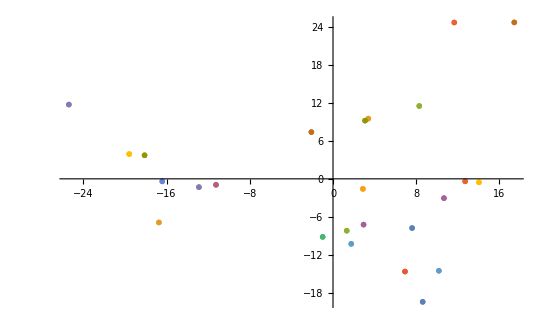

```mathematica
characterImagesReduced = DimensionReduce[characterImagesSampled];
ListPlot[
List/@characterImagesReduced,
PlotMarkers->(Image[#,ImageSize->40]& /@ characterImagesSampled)
]
```

```mathematica
characterData=RandomSample[Flatten[Thread/@Thread[characterImages->characters]]];
characterClassifier=Classify[characterData]
```

ClassifierFunction[…]

```mathematica
characterClassifier[-Graphics-](*战国文字*)
```

篆文

```mathematica
ReverseSort@characterClassifier[-Graphics-,"Probabilities"]
```

<|甲骨文→0.996989,隶书→0.00301079,篆文→1.14565×10^-8,周代金文→1.33252×10^-17,楷书→1.43602×10^-31|>

```mathematica
characterClassifier[-Graphics-](*《甲骨文合集》27021（《国博》203）*)
```

甲骨文